# DarkMoreEverything

## By: Tone

## Introduction

The aim of this project is to have complete dark mode throughout all of Mathematica and its components that does not restrict any features or functionality. While project has not yet reached complete coverage, it far exceeds the coverage of all other dark themes publicly available, and has no functionality constraints. The project has also evolved to include front end functionality extensions and improvements.

## Cell style examples

# Title [ Alt+1 ]

## Subtitle [ Alt+2 ]

## Chapter [ Alt+3 ]

## Section [ Alt+4 ]

### Subsection [ Alt+5 ]

#### Subsubsection [ Alt+6 ]

##### Subsubsubsection

Text [ Alt + 7 ]

Item [ Text+Tab | Text+* | Subitem+Backspace ]

Subitem [ Item+Tab | Item+* | Subsubitem+Backspace ]

Subsubitem [ Subitem+Tab | Subitem+* ]

```mathematica
"Code [ Alt+8 | Input+` ]"
```

"InitialisationCell [ Code+Tab ]"

InitialisationCell [ Code+Tab ]

```mathematica
"Input [ Alt+9 | Code+` ]"
```

Print

Echo

EchoTiming

Output

For the delimiter above [ Input+- ]

ExternalLanguage [ Input+> ]

NLInput [ Input+= ]

WolframAlphaInput [ NLInput+= ]

## Example outputs

## Entities

```mathematica
Quantity[12, "Meters"]
```

```mathematica
Entity["Country","UnitedKingdom"][EntityProperty["Country","AdministrativeDivisions"]]
```

```mathematica
EntityClass["Country","EuropeanUnion"][EntityPropertyClass["Country","EconomicProperties"]]
```

## Dataset

```mathematica
ExampleData[{"Dataset","Planets"}]
```

## Plots

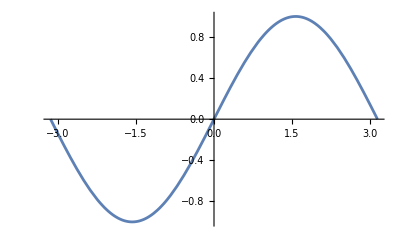

```mathematica
Plot[Sin[x],{x,-Pi,Pi}]
```

## Manipulate

```mathematica
Manipulate[]
```

## NaturalLanguageInput

WolframAlphaQueryParseResults

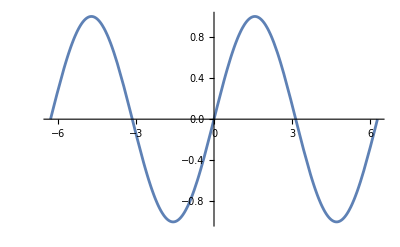

## WolframAplphaInput

Denmark

WolframAlphaQueryResults

## Context coloring

Quiet[
	Other`Symbol=0;
	Global`Symbol=0;
]

Global`Symbol::shdw: Symbol Symbol appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

```mathematica
Undefined`Symbol
System`Symbol
Global`Symbol
Other`Symbol
```

## Extended coverage

## Documentation

The following links showcase some of the changes to the documentation:

Function documentation

Entity documentation

Tech Notes

Monographs

## Message window

```mathematica
(*
	Evaluation of this cell generates a
	message inside the message window
*)
SessionSubmit[
	1/0
];
```

## Wolfram Chatbooks

```mathematica
CreateNotebook["ChatEnabled"];
```

## MUnit tests

```mathematica
CreateNotebook["Testing"];
```

## Stylesheet theming

```mathematica
SystemOpen@
FileNameJoin[{$InstallationDirectory,"SystemFiles","FrontEnd","StyleSheets","DarkModeEverything.nb"}]
```

## Handy additions

## Map subscript level-spec

```mathematica
(* f(/@)_i list -> Map[f, list, {i}] *)
f (/@)_2 {1,1,{2,{3,3}}}
```

{1,1,{f[2],f[{3,3}]}}